```mathematica
ImageTake[-Graphics-,-50+{340,370},+170+{330,360}]
```

-Graphics-

```mathematica
ImageDimensions[-Graphics-]
```

{848,480}

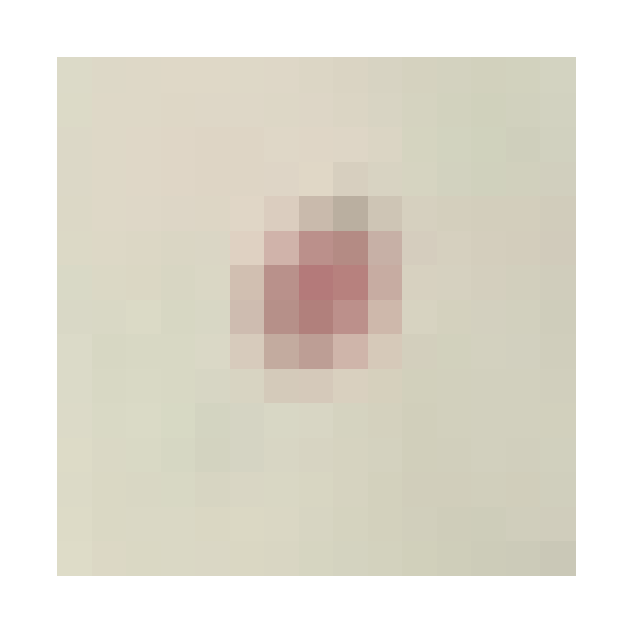

```mathematica
slikapiksli=(Delete[#,-1]&/@#)&/@ImageData[ImageResize[-Graphics-,15]];
Show[
Table[

Graphics[{
RGBColor[slikapiksli[[y,x]]  ],
EdgeForm[],

Polygon[{
{x,y},
{x+1,y},
{x+1,y+1},
{x,y+1}
}]
}],

{y,Length[slikapiksli]},
{x,Length[slikapiksli[[1]] ]}
]
]
```

```mathematica
slikapiksli=(Delete[#,-1]&/@#)&/@ImageData[ImageResize[-Graphics-,15]];
Show[
Table[
trenutnabarva=slikapiksli[[y,x]];
Graphics3D[{
RGBColor[trenutnabarva],
Arrowheads[.01],
Arrow[Tube[{{x+.5,y+.5,0},{x+.5,y+.5,0}+trenutnabarva},
.02]]
}]
,

{y,Length[slikapiksli]},
{x,Length[slikapiksli[[1]] ]}
],

Table[

Graphics3D[{
RGBColor[slikapiksli[[y,x]]  ],
EdgeForm[Thin],

Polygon[{
{x,y,0},
{x+1,y,0},
{x+1,y+1,0},
{x,y+1,0}
}]
}],

{y,Length[slikapiksli]},
{x,Length[slikapiksli[[1]] ]}
],
Boxed->False,
Lighting->"Neutral",
Background->White
(*ImageSize->4{1920,1080}*)
]
```

-Graphics3D-

```mathematica
Export["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\RGB vektorji2.png",%]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\RGB vektorji2.png

```mathematica
slikapiksli=(Delete[#,-1]&/@#)&/@ImageData[-Graphics-];
rzanke=3;
srzanke={10,10};

grafikakvadratkov=Show[
Table[

Graphics[{
RGBColor[slikapiksli[[y,x]]  ],
EdgeForm[],

Polygon[{
{x,y},
{x+1,y},
{x+1,y+1},
{x,y+1}
}]
}],

{y,Length[slikapiksli]},
{x,Length[slikapiksli[[1]] ]}
]];
Manipulate[

Show[
grafikakvadratkov,
Graphics[{
RGBColor[{1,1,0,.3}],
EdgeForm[{RGBColor[{1,1,0,1}],Thickness[.005]}],
Polygon[{
#,
#+{1,0},
#+{1,1},
#+{0,1}
}]
}]&/@If[rzanke==0,
{srzanke},
((srzanke+#)&/@Join[
Table[{x,rzanke},{x,-rzanke,rzanke-1,1}],
Table[{rzanke,y},{y,rzanke,-rzanke+1,-1}],
Table[{x,-rzanke},{x,rzanke,-rzanke+1,-1}],
Table[{-rzanke,y},{y,-rzanke,rzanke-1,1}]
])]
],



{rzanke,0,5,1}]
```

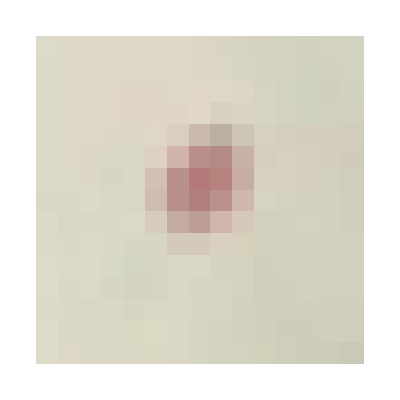

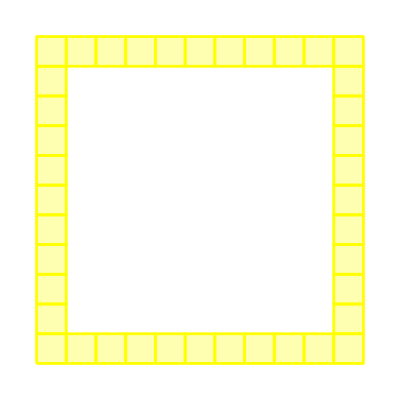

```mathematica
rzanke=5;
Show[
Graphics[{
RGBColor[{1,1,0,.3}],
EdgeForm[{RGBColor[{1,1,0,1}],Thickness[.005]}],
Polygon[{
#,
#+{1,0},
#+{1,1},
#+{0,1}
}]
}]&/@If[rzanke==0,
{srzanke},
((srzanke+#)&/@Join[
Table[{x,rzanke},{x,-rzanke,rzanke-1,1}],
Table[{rzanke,y},{y,rzanke,-rzanke+1,-1}],
Table[{x,-rzanke},{x,rzanke,-rzanke+1,-1}],
Table[{-rzanke,y},{y,-rzanke,rzanke-1,1}]
])]
]
```

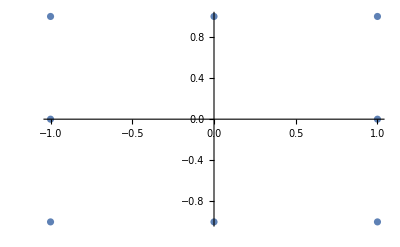

```mathematica
ListPlot[{{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1},{-1,-1},{-1,0}}]
```

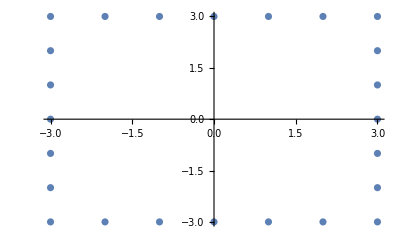

```mathematica
ListPlot[{{-3,3},{-2,3},{-1,3},{0,3},{1,3},{2,3},{3,3},{3,2},{3,1},{3,0},{3,-1},{3,-2},{3,-3},{2,-3},{1,-3},{0,-3},{-1,-3},{-2,-3},{-3,-3},{-3,-2},{-3,-1},{-3,0},{-3,1},{-3,2}}]
```